# The Energy Function of ^163 Lu

## A quantitative study on the evolution of numerical values of ℋ w.r.t. the spherical coordinates and “free” terms

## ℋ=I/2(A_1+A_2)+A_3 I^2+I(I-1/2)sin^2 θ(A_1 cos^2 φ+A_2 sin^2 φ-A_3)+j/2(A_2+A_3)+A_1 j^2-2 A_1 Ij sinθ-V(2j-1)/(j+1)sin(γ+π/6);

## Energy function

```mathematica
(*Hen[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ*π/180]^2(A1*Cos[φ*π/180]^2+A2*Sin[φ*π/180]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ*π/180]-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];*)
Hen[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ]^2(A1*Cos[φ]^2+A2*Sin[φ]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ]-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
```

## Numerical values of H as a function of the coordinates (@fixed parameters)

```mathematica
(*Do[Print[th," ",Hen[spinTSD1,π/2,th,A1,A2,A3,V,γ]],{th,{0,π/4,π/2,π}}]*)
```

## T0=free term

## T1=mixed term f(θ,φ)

## T2=theta term g(θ)

```mathematica
IF[i_]:=1/(2i);
t0[I_,j_,a1_,a2_,a3_,V_,γ_]:=I/2(a1+a2)+a3*I^2+j/2(a2+a3)+a1*j^2-V(2j-1)/(j+1)Sin[γ+π/6];
t1[I_,a1_,a2_,a3_,θ_,φ_]:=I(I-1/2)Sin[θ]^2(a1*Cos[φ]^2+a2*Sin[φ]^2-a3);
t2[I_,j_,a1_,θ_]:=-2*a1*I*j*Sin[θ];
```

## Study each term

### Spins & constants

```mathematica
spin1=N[25/2];
spin2=N[31/2];
spin3=N[37/2];
spin4=N[51/2];
j=13/2;
```

### Fit parameters (which could result unto a valid contour plot with minima)

```mathematica
i1=52;i2=32;i3=48;v=9.1;γ=15;
```

## Setting up the minimal angles (spherical coordinates θ and φ (different for each parameter set)

```mathematica
θm=90;Subscript[φ, 1]=0;Subscript[φ, 2]=180;Subscript[φ, 3]=360;
```

## T_0 - evolution with γ

```mathematica
p1[i1_,i2_,i3_,v_]:=Plot[{t0[spin1,j,IF[i1],IF[i2],IF[i3],v,gm],t0[spin2,j,IF[i1],IF[i2],IF[i3],v,gm],t0[spin3,j,IF[i1],IF[i2],IF[i3],v,gm],t0[spin4,j,IF[i1],IF[i2],IF[i3],v,gm]},{gm,0,π/3},Frame->True,Axes->False,FrameLabel->{"γ [rad]","T_0"},FrameStyle->Directive[Black,Thick],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},AspectRatio->1,PlotLegends->{"I_TSD1","I_TSD2","I_TSD3","I_TSD4"},PlotLabel->StringTemplate["T_0 - evolution with γ \n @ℐ_1=`` ℐ_2=`` ℐ_3=`` V=``"][i1,i2,i3,v]];
```

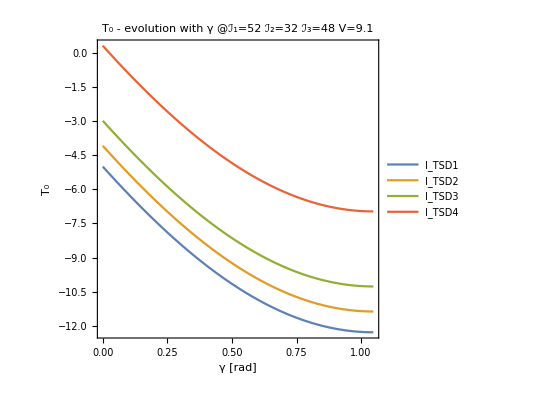

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/T0_gm.jpeg",p1[i1,i2,i3,v]];
Show[p1[i1,i2,i3,v]]
```

## T_0 - evolution with V

```mathematica
p2[i1_,i2_,i3_,gm_]:=Plot[{t0[spin1,j,IF[i1],IF[i2],IF[i3],v,gm*π/180],t0[spin2,j,IF[i1],IF[i2],IF[i3],v,gm*π/180],t0[spin3,j,IF[i1],IF[i2],IF[i3],v,gm*π/180],t0[spin4,j,IF[i1],IF[i2],IF[i3],v,gm*π/180]},{v,0,10},Frame->True,Axes->False,FrameLabel->{"V [MeV]","T_0"},FrameStyle->Directive[Black,Thick],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},AspectRatio->1,PlotLegends->{"I_TSD1","I_TSD2","I_TSD3","I_TSD4"},PlotLabel->StringTemplate["T_0 - evolution with V \n @ℐ_1=`` ℐ_2=`` ℐ_3=`` γ=``"][i1,i2,i3,gm]];
```

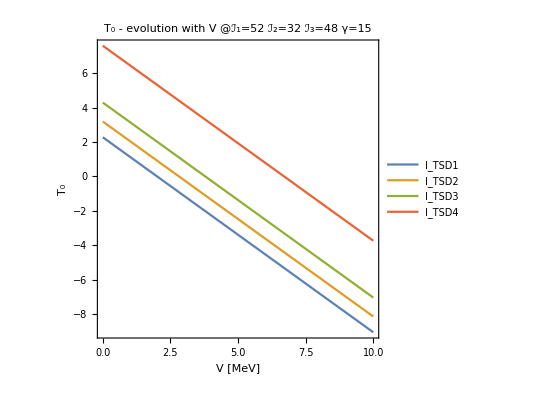

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/T0_V.jpeg",Show[p2[i1,i2,i3,γ]]];
Show[p2[i1,i2,i3,γ]]
```

## T_1 - evolution with the coordinates

### evolution with θ

```mathematica
t1plot1[i1_,i2_,i3_,φ_]:=Plot[{t1[spin1,IF[i1],IF[i2],IF[i3],th,φ],t1[spin2,IF[i1],IF[i2],IF[i3],th,φ],t1[spin3,IF[i1],IF[i2],IF[i3],th,φ],t1[spin4,IF[i1],IF[i2],IF[i3],th,φ]},{th,0,π},Frame->True,Axes->False,FrameLabel->{"θ [rad]","T_1"},FrameStyle->Directive[Black,Thick],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},AspectRatio->1,PlotLegends->{"I_TSD1","I_TSD2","I_TSD3","I_TSD4"},PlotLabel->StringTemplate["T_1 - evolution with θ \n @ℐ_1=`` ℐ_2=`` ℐ_3=`` φ=``"][i1,i2,i3,φ*180/π]];
```

### Evolution with the first minimum point

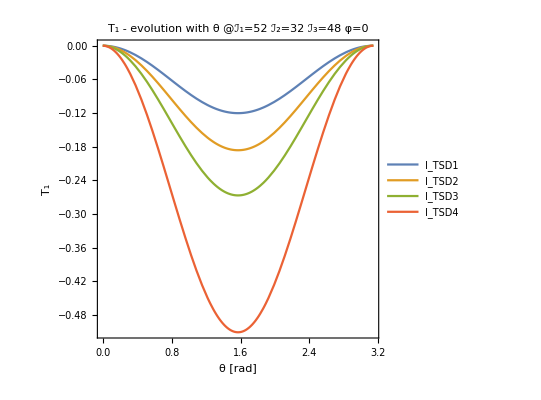

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/T1_th.jpeg",Show[t1plot1[i1,i2,i3,Subscript[φ, 1]*π/180]]];
Show[t1plot1[i1,i2,i3,Subscript[φ, 1]*π/180]]
```

```mathematica
Evolution with the second minimum point
```

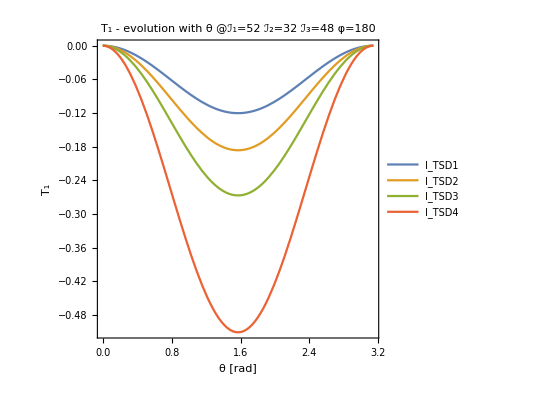

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/T1_th.jpeg",Show[t1plot1[i1,i2,i3,Subscript[φ, 2]*π/180]]];
Show[t1plot1[i1,i2,i3,Subscript[φ, 2]*π/180]]
```

```mathematica
Evolution with the third minimum point
```

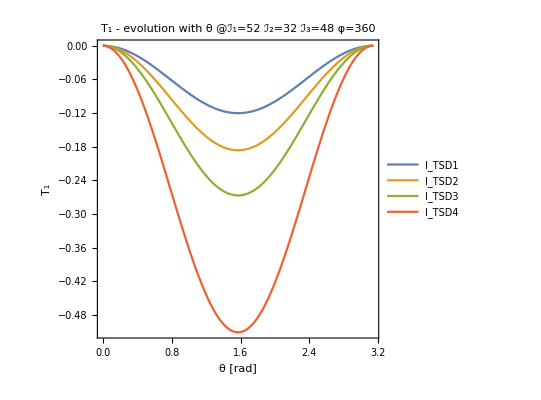

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/T1_th.jpeg",Show[t1plot1[i1,i2,i3,Subscript[φ, 3]*π/180]]];
Show[t1plot1[i1,i2,i3,Subscript[φ, 3]*π/180]]
```

### evolution with φ

```mathematica
t1plot2[i1_,i2_,i3_,θ_]:=Plot[{t1[spin1,IF[i1],IF[i2],IF[i3],θ,fi],t1[spin2,IF[i1],IF[i2],IF[i3],θ,fi],t1[spin3,IF[i1],IF[i2],IF[i3],θ,fi],t1[spin4,IF[i1],IF[i2],IF[i3],θ,fi]},{fi,0,2π},Frame->True,Axes->False,FrameLabel->{"φ [rad]","T_1"},FrameStyle->Directive[Black,Thick],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},AspectRatio->1,PlotLegends->{"I_TSD1","I_TSD2","I_TSD3","I_TSD4"},PlotLabel->StringTemplate["T_1 - evolution with φ \n @ℐ_1=`` ℐ_2=`` ℐ_3=`` θ=``"][i1,i2,i3,θ*180/π]];
```

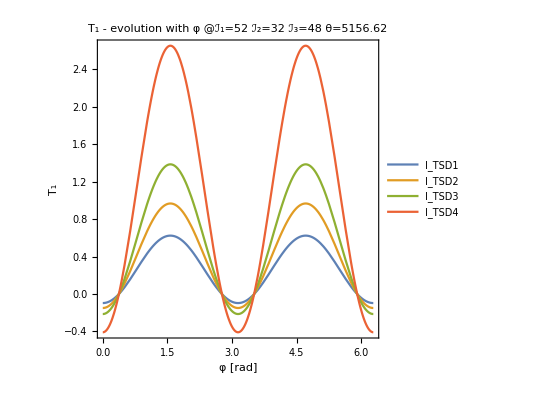

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/T1_fi.jpeg",Show[t1plot2[i1,i2,i3,θm*π/180]]];
Show[t1plot2[i1,i2,i3,θm]]
```

## T_2 - evolution with θ

```mathematica
t2plot[i1_]:=Plot[{t2[spin1,j,IF[i1],th],t2[spin2,j,IF[i1],th],t2[spin3,j,IF[i1],th],t2[spin4,j,IF[i1],th]},{th,0,π},Frame->True,Axes->False,FrameLabel->{"θ [rad]","T_2"},FrameStyle->Directive[Black,Thick],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},AspectRatio->1,PlotLegends->{"I_TSD1","I_TSD2","I_TSD3","I_TSD4"},PlotLabel->StringTemplate["T_2 - evolution with θ \n @ℐ_1=``"][i1]];
```

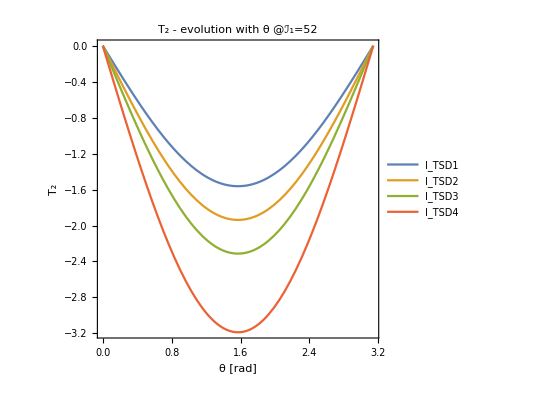

```mathematica
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/T2_th.jpeg",Show[t2plot[i1]]];
Show[t2plot[i1]]
```

## Contour plot - T_1+T_2

```mathematica
cpT12[I_,i1_,i2_,i3_]:=ContourPlot[t1[I,IF[i1],IF[i2],IF[i3],θ,φ]+t2[I,j,IF[i1],θ],{θ,0,π},{φ,0,2π},AspectRatio->Automatic,PlotLegends->Automatic,Contours->5];
Show[cpT12[spin1,i1,i2,i3]]
```

-Graphics-

## Contour plot - T_1

```mathematica
cpT1[I_,i1_,i2_,i3_]:=ContourPlot[t1[I,IF[i1],IF[i2],IF[i3],θ,φ],{θ,0,π},{φ,0,2π},AspectRatio->Automatic,PlotLegends->Automatic,Contours->5];
Show[cpT1[spin1,i1,i2,i3]]
```

-Graphics-

```mathematica
(*Manipulate[Do[Print[N[t1[spin,IF[i1Fit],IF[i2Fit],IF[i3Fit],θ,φ]]," ",N[t1[spin,IF[i1Fit],IF[i2Fit],IF[i3Fit],θ,φ]+t2[spin,j,IF[i1Fit],θ]]],{spin,6.5,30.5,2}],{θ,0,π},{φ,0,2π}]*)
```

```mathematica
Manipulate[Style[StringTemplate["``\n``"][t1[spin1,IF[i1Fit],IF[i2Fit],IF[i3Fit],θ,φ],t1[spin1,IF[i1Fit],IF[i2Fit],IF[i3Fit],θ,φ]+t2[spin1,j,IF[i1Fit],θ]],Red],{θ,0,π},{φ,0,2π}]
```

```mathematica
Manipulate[ContourPlot[t1[spin1,IF[i1],IF[i2],IF[i3],θ,φ],{θ,0,π},{φ,0,2π},Frame->True,FrameStyle->Directive[Black,Thick],Contours->11,FrameLabel->{"θ","φ"},PlotLabel->StringTemplate["I=``"][spin1],LabelStyle->{15,Black,Bold,FontFamily->"Times New Roman"},ImageSize->Medium,AspectRatio->Automatic,PlotLegends->Automatic],{i1,1,120,1},{i2,1,120,1},{i3,1,120,1}]
```